Numerical Relativity Hub | Educative Notebooks | 17 . OCT . 2024 | Amir H. Ebrahimnezhad (github, email)

# Galerkin Method

## > Numerical Methods

## Introduction

The Galerkin method is a numerical approach to solve differential equations by approximating the solution using a linear combination of basis functions . The method ensures that the residual (error) is orthogonal to the space spanned by the chosen basis functions . In this notebook we would try to solve a differential equation using this method, for a more detailed note on how the method actually works check the docs folder for Galerkin Method.md:

```mathematica
differentialEquation=D[u[x],{x,2}]==-1;
boundaryConditions = {u[0] ==0, u[1]== 0};
```

## Using the Method

Choose Basis Functions: For the Galerkin method, we choose basis functions that satisfy the boundary conditions. Common choices are polynomials that vanish at the boundaries. Let’s select the following two basis functions:

```mathematica
phi1[x_]:=x (1-x)
phi2[x_]:=x^2 (1-x)^2
```

Approximate the Solution: The approximate solution 𝑢(𝑥) is represented as a linear combination of the chosen basis functions:

```mathematica
uApprox[x_]:=c1 phi1[x]+c2 phi2[x]
```

Define the Residual: The residual is the error that remains when the approximate solution is substituted into the original differential equation. The goal of the Galerkin method is to minimize this residual.

```mathematica
residual=D[uApprox[x],{x,2}]+1;
```

Project the Residual onto the Basis Functions: The key idea in the Galerkin method is to make the residual orthogonal to each basis function. This leads to a system of equations, which we solve for the coefficients c_1 and c_2 We enforce orthogonality by integrating the residual multiplied by each basis function and setting it to zero:

```mathematica
eqn1=Integrate[residual*phi1[x],{x,0,4}]==0;
eqn2=Integrate[residual*phi2[x],{x,0,4}]==0;
```

Solve for the Coefficients: Mathematica’s Solve function will give us the values of the unknown coefficients

```mathematica
sol=Solve[{eqn1,eqn2},{c1,c2}] // Transpose //MatrixForm
```

(c1→1/2
c2→0)

## Substitution and Plot:

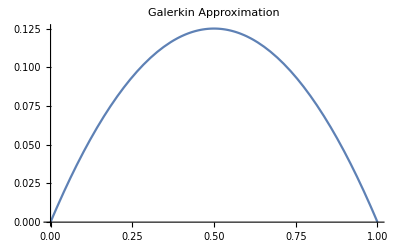

```mathematica
uSol[x_]:=uApprox[x]/. sol;
Plot[uSol[x],{x,0,1},PlotLabel->"Galerkin Approximation",PlotRange->All]
```